#### Iniziamo con un reminder sulla rappresentazione del fascio

```mathematica
(*  Partiamo dalla matrice sigma (a meno dell'emittanza fattorizzata)  *)
MT={{γ,α},{α,β}};
Print["Twiss Matrix -> ",MatrixForm[MT]]
Print["Beam Quadratic Form -> ",Simplify[{x,xp}.MT.{x,xp}]//TraditionalForm]

(* e definiamo la matrice di normalizzazione con la sua inversa *)

NM={{1/Sqrt[β],0},{α/Sqrt[β],Sqrt[β]}};
NMI={{Sqrt[β],0},{-α/Sqrt[β],1/Sqrt[β]}};
Print["Normalization Matrix         -> ",MatrixForm[NM]]
Print["Inverse Normalization Matrix -> ",MatrixForm[NMI]]
Print["Product Verification         -> ",MatrixForm[NMI.NM]]

(* 
le coordinate normalizzate sono {XN,YN}=NM.{x,y}. Verifichiamo che l'ellissi diventa un cerchio 
2 x y α+y^2 β+x^2 γ -> XN^2+YN^2 
*)

Simplify[{XN,XPN}.Transpose[NMI].MT.NMI.{XN,XPN}]/.γ->(1+α^2)/β

 (*
a questo punto data una ampiezza ottengo le coordinate normalizzate da coseno e seno della fase 
e e coordinate reali con la matrice inversa. Per una ampiezza A (= Sqrt[emittance]) 
*)

NMI.{A Cos[θ], A Sin[θ]}
```

Twiss Matrix -> (γ | α
α | β)

Beam Quadratic Form -> γ x^2+2 α x xp+β xp^2

Normalization Matrix         -> (1/(√β) | 0
α/(√β) | √β)

Inverse Normalization Matrix -> (√β | 0
-α/(√β) | 1/(√β))

Product Verification         -> (1 | 0
0 | 1)

XN^2+XPN^2

{{{0.+0.000359102 √β,0.-0.000046116 √β,0.+0.0000152499 √β,0.+0.0000338012 √β,0.-0.000170054 √β},29998,{0.+0.0000828333 √β,3,0.-23 √β}},{1}}
 |  |  |  |

#### definiamo i parametri del fascio Al setto elettrostatico di estrazione abbiamo

```mathematica
7.14/5
```

1.428

```mathematica
epsxrms=1.428 10^-6;
epsx=5epsxrms;
betx=16.14922287;
alfx=0.3870055822;
gamx=(1+alfx^2)/betx;
Dx=3.9445233385;
Dxp=-0.6286237454;

NMIx={{Sqrt[betx],0},{-alfx/Sqrt[betx],1/Sqrt[betx]}};

epsyrms=1.428 10^-6;
epsy=5epsyrms;
bety=7.629957552;
alfy=-0.2646797343;
gamy=(1+alfy^2)/bety;
Dy=0.0;
Dyp=0.0;

NMIy={{Sqrt[bety],0},{-alfy/Sqrt[bety],1/Sqrt[bety]}};
```

### Generation test

#### Generiamo la distribuzione radiale per un fascio gaussiano Define radial distribution and generate value set. Define centered and with unit sigma.

Piecewise[{{ⅇ^(-x^2/2) x, x>0}, {0, True}}]

{0.393469,0.5,0.864665,0.917915,0.988891,0.999996}

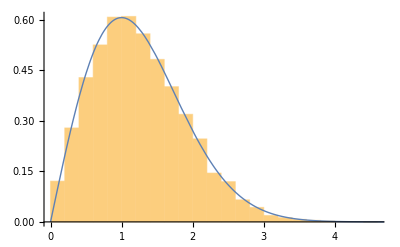

```mathematica
(*
𝒟=ProbabilityDistribution[2π (x-μ)/(2π σ^2) Exp[-(x-μ)^2/(2σ^2)]/.{μ->0,σ->1},{x,μ,Infinity}];
*)
𝒟=ProbabilityDistribution[2π x/(2π σ^2) Exp[-(x)^2/(2σ^2)]/.{σ->1},{x,0,Infinity}];

PDF[𝒟,x]

Integrate[PDF[𝒟,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5],3,5}//N

amplitudex=RandomVariate[𝒟,10^4];
amplitudey=RandomVariate[𝒟,10^4];

Show[
Histogram[amplitudex,20,"ProbabilityDensity"],
Plot[PDF[𝒟,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

#### From radial distribution generate position in normalised phase space. Amplitude goes with Sqrt[RMS emittance]

```mathematica
coorx={};
Do[θ=RandomReal[{0,2π}];AppendTo[coorx,amplitudex[[n]]*Sqrt[epsxrms]*NMIx.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudex]}]

coory={};
Do[θ=RandomReal[{0,2π}];AppendTo[coory,amplitudey[[n]]*Sqrt[epsyrms]*NMIy.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudey]}]
```

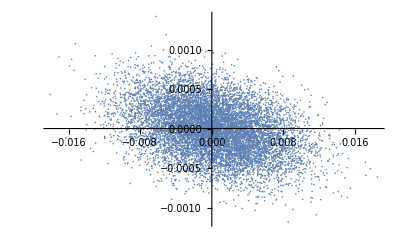

```mathematica
ListPlot[coorx]
```

#### Passiamo alla generazione di un fascio omogeneo 2D

Piecewise[{{(2 x)/5, 0<x<√5}, {0, True}}]

{0.2,0.277259,0.8,1.,1.,1.}

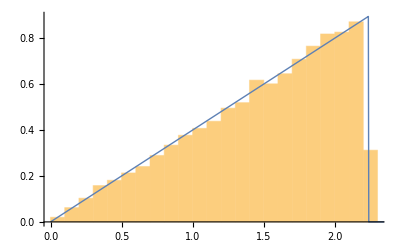

```mathematica
𝒟=ProbabilityDistribution[2π x/(π R^2),{x,0,R}]/.{R->Sqrt[5]};

PDF[𝒟,x]

Integrate[PDF[𝒟,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5],3,5}//N

amplitudex=RandomVariate[𝒟,10^4];
amplitudey=RandomVariate[𝒟,10^4];

Show[
Histogram[amplitudex,20,"ProbabilityDensity"],
Plot[PDF[𝒟,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

#### From radial distribution generate position in normalised phase space. Amplitude goes with Sqrt[RMS emittance]

```mathematica
coorx={};
Do[θ=RandomReal[{0,2π}];AppendTo[coorx,amplitudex[[n]]*Sqrt[epsxrms]*NMIx.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudex]}]

coory={};
Do[θ=RandomReal[{0,2π}];AppendTo[coory,amplitudey[[n]]*Sqrt[epsyrms]*NMIy.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudey]}]
```

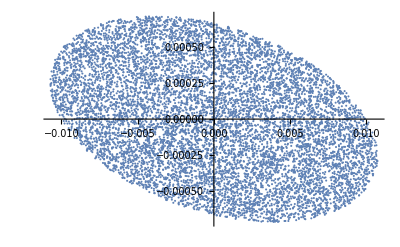

```mathematica
ListPlot[coorx]
```

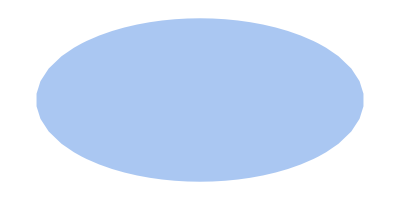

```mathematica
ℛ=ImplicitRegion[(x/2)^2+y^2≤1,{x,y}];
Region[ℛ]
```

```mathematica
pts=RandomPoint[ℛ,5000];
```

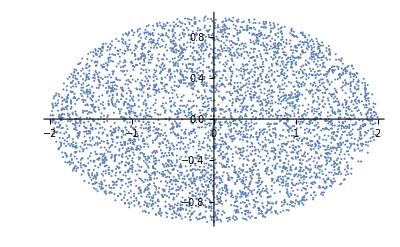

```mathematica
ListPlot[pts]
```

```mathematica
DirichletDistribution
```

DirichletDistribution

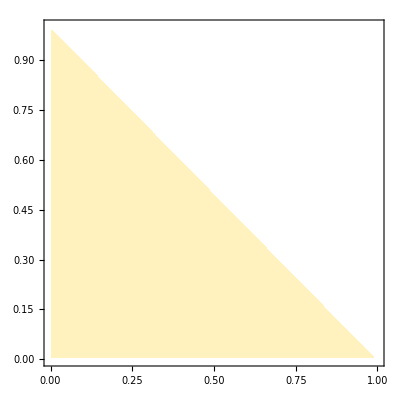

```mathematica
ContourPlot[PDF[DirichletDistribution[{ 1,1,1}],{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y<1]]
```

### Generate Flat/Gaussian beam

Genero (N * 1/0.91) particelle distribuite in modo gaussiano in modo da averne 
N dentro a una emittanza 5 e_rms 
(dentro a 5 e_rms cade il 91.79 delle particelle generate)

#### Generiamo una distribuzione gaussiana in y e piatta in x (~MTI) Genero anche una distribuzione uniforme in Dp/p

Piecewise[{{ⅇ^(-x^2/2) x, x>0}, {0, True}}]

{0.393469,0.5,0.864665,0.917915}

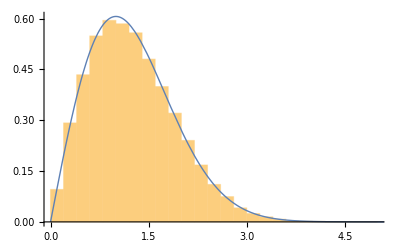

```mathematica
𝒟𝒢=ProbabilityDistribution[2π x/(2π σ^2) Exp[-(x)^2/(2σ^2)]/.{σ->1},{x,0,Infinity}];

PDF[𝒟𝒢,x]

Integrate[PDF[𝒟𝒢,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5]}//N

amplitudey=RandomVariate[𝒟𝒢,3 10^4];

Show[
Histogram[amplitudey,20,"ProbabilityDensity"],
Plot[PDF[𝒟𝒢,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

Piecewise[{{(2 x)/5, 0<x<√5}, {0, True}}]

{0.2,0.277259,0.8,1.,1.,1.}

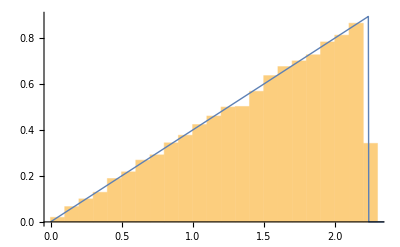

```mathematica
𝒟ℱ=ProbabilityDistribution[2π x/(π R^2),{x,0,R}]/.{R->Sqrt[5]};

PDF[𝒟ℱ,x]

Integrate[PDF[𝒟ℱ,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5],3,5}//N

amplitudex=RandomVariate[𝒟ℱ,3 10^4];

Show[
Histogram[amplitudex,20,"ProbabilityDensity"],
Plot[PDF[𝒟ℱ,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

```mathematica
coorx={};
Do[θ=RandomReal[{0,2π}];AppendTo[coorx,amplitudex[[n]]*Sqrt[epsxrms]*NMIx.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudex]}]

coory={};
Do[θ=RandomReal[{0,2π}];AppendTo[coory,amplitudey[[n]]*Sqrt[epsyrms]*NMIy.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudey]}]
```

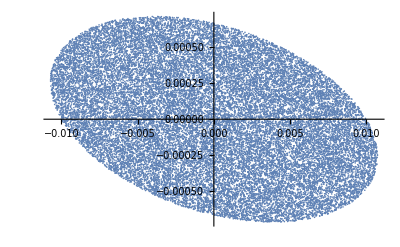

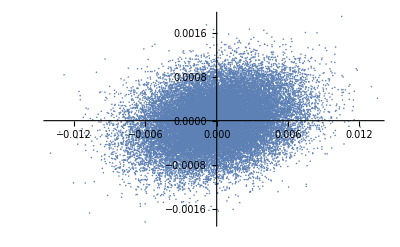

```mathematica
ListPlot[coorx]
ListPlot[coory]
```

UniformDistribution[{-0.004,-0.001}]

Piecewise[{{333.333, -0.004≤x≤-0.001}, {0, True}}]

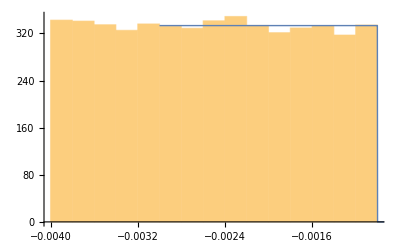

```mathematica
𝒟ℳ=UniformDistribution[{-0.004,-0.001}]

PDF[𝒟ℳ,x]

amplitudep=RandomVariate[𝒟ℳ,3 10^4];

Show[
Histogram[amplitudep,20,"ProbabilityDensity"],
Plot[PDF[𝒟ℳ,x]/.{σ->1},{x,-0.003,0.003},PlotStyle->Thick]]
```

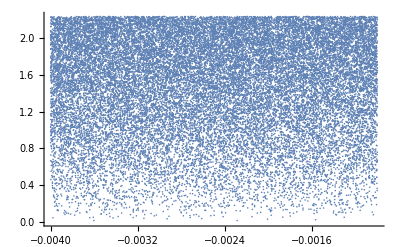

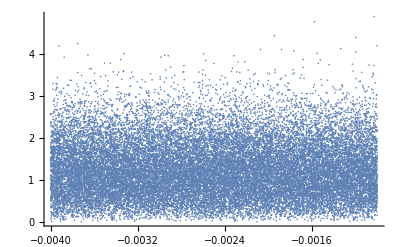

```mathematica
ListPlot[Transpose[{amplitudep,amplitudex}]]
ListPlot[Transpose[{amplitudep,amplitudey}]]
```

```mathematica
Ax=Sqrt[gamx*#[[1]]^2+2*alfx*#[[1]]*#[[2]]+betx*#[[2]]^2]&/@coorx;
```

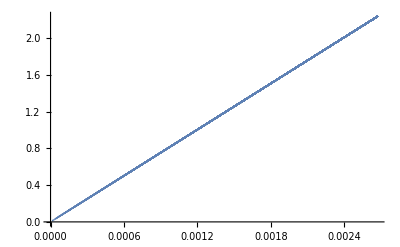

```mathematica
ListPlot[Transpose[{Ax,amplitudex}]]
```

```mathematica
coorx[[1;;3]]
```

{{-0.0100832,0.000308069},{0.000449087,0.000502152},{-0.00060759,-0.000503792}}

#### Check statistical quantities from distribution

```mathematica
x2=Mean[coorx[[;;,1]]^2];
xp2=Mean[coorx[[;;,2]]^2];
xxp=Mean[coorx[[;;,1]]*coorx[[;;,2]]];

y2=Mean[coory[[;;,1]]^2];
yp2=Mean[coory[[;;,2]]^2];
yyp=Mean[coory[[;;,1]]*coory[[;;,2]]];
```

```mathematica
epsStatx=Sqrt[x2*xp2-xxp^2]
betaStatx=x2/Sqrt[x2*xp2-xxp^2]
alfaStatx=-xxp/Sqrt[x2*xp2-xxp^2]
epsxrms
betx
alfx

epsStaty=Sqrt[y2*yp2-yyp^2]
betaStaty=y2/Sqrt[y2*yp2-yyp^2]
alfaStaty=-yyp/Sqrt[y2*yp2-yyp^2]
epsyrms
bety
alfy
```

1.78918×10^-6

16.2284

0.385751

1.428×10^-6

16.1492

0.387006

1.43668×10^-6

7.54048

-0.266396

1.428×10^-6

7.62996

-0.26468

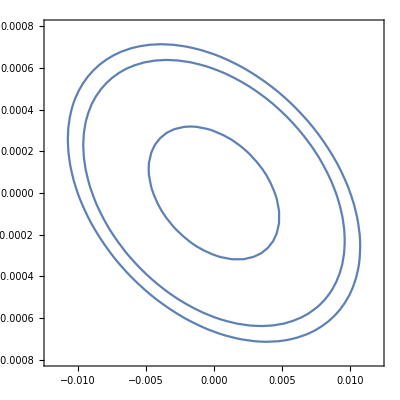

```mathematica
ContourPlot[gamx*x^2+2*alfx*x*xp+betx*xp^2=={epsxrms,4epsxrms,5epsxrms},{x,-2.5*Sqrt[epsxrms*betx],2.5*Sqrt[epsxrms*betx]},{xp,-2.5*Sqrt[epsxrms*gamx],2.5*Sqrt[epsxrms*gamx]}]
```

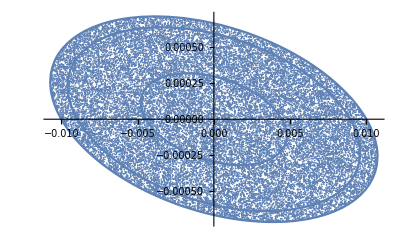

```mathematica
Show[ListPlot[coorx],ContourPlot[gamx*x^2+2*alfx*x*xp+betx*xp^2=={epsxrms,4epsxrms,5epsxrms},{x,-2.5*Sqrt[epsxrms*betx],2.5*Sqrt[epsxrms*betx]},{xp,-2.5*Sqrt[epsxrms*gamx],2.5*Sqrt[epsxrms*gamx]}]]
```

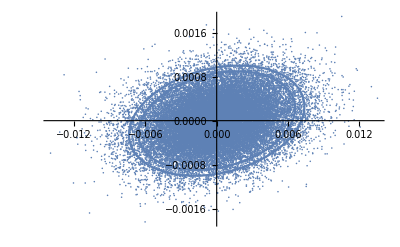

```mathematica
Show[ListPlot[coory],ContourPlot[gamy*y^2+2*alfy*y*yp+bety*yp^2=={epsyrms,4epsyrms,5epsyrms},{y,-2.5*Sqrt[epsyrms*bety],2.5*Sqrt[epsyrms*bety]},{yp,-2.5*Sqrt[epsyrms*gamy],2.5*Sqrt[epsyrms*gamy]}]]
```

```mathematica
s1=Select[coory,gamy*#[[1]]^2+2*alfy*#[[1]]*#[[2]]+bety*#[[2]]^2<5*epsyrms &];
Length[s1]
Length[coory]
```

27513

30000

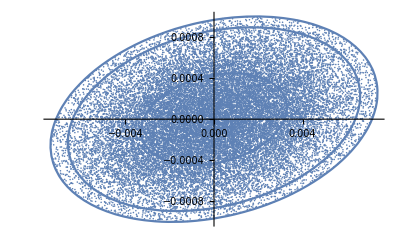

```mathematica
Show[ListPlot[s1],ContourPlot[gamy*y^2+2*alfy*y*yp+bety*yp^2=={epsyrms,4epsyrms,5epsyrms},{y,-2.5*Sqrt[epsyrms*bety],2.5*Sqrt[epsyrms*bety]},{yp,-2.5*Sqrt[epsyrms*gamy],2.5*Sqrt[epsyrms*gamy]}],PlotRange->All]
```

```mathematica
f[x_,n_]:=StringTake["                   "<>ToString[Row[{PaddedForm[MantissaExponent[N[x]][[1]],n,NumberPadding->{" ","0"}],"E",MantissaExponent[x][[2]]}]],-19]

f[-π/1000,{10,10}]
```

-0.3141592654E-2

```mathematica
(*A=Transpose[Join[Transpose[coorx[[1;;1000]]],Transpose[coory[[1;;1000]],amplitudep[[1;;1000]]]]];*)
A=Transpose[Join[Transpose[coorx],Transpose[coory],{amplitudep}]];
Take[A,10]
A[[9999]]
ListPlot[A[[;;,{1,2}]]]
ListPlot[A[[;;,{3,4}]]]
```

{{-0.0100832,0.000308069,-0.00207679,0.000275416,-0.00307255},{0.000449087,0.000502152,-0.00584761,-0.0000666548,-0.00191325},{-0.00060759,-0.000503792,-0.00182589,0.000743778,-0.00200903},{-0.00107526,0.0000367876,0.00524248,0.000217616,-0.00163817},{0.00459764,0.000293599,-0.00134219,0.000449694,-0.00385412},{0.00125096,0.000246537,-0.00248207,0.0001442,-0.00126541},{0.00464912,-0.000169631,-0.00199962,0.0000558131,-0.00167037},{-0.00763633,0.00017701,0.00244201,-0.000214327,-0.00366558},{-0.00618516,0.000619218,0.00303899,-0.0000266124,-0.00154582},{-0.00429679,0.000686045,0.00508691,-0.000205148,-0.00377696}}

{0.00835121,0.000173455,0.00523177,0.0000101574,-0.00202323}

-Graphics-

-Graphics-

```mathematica
SetDirectory["C:\\Users\\enrico.felcini\\Desktop\\TestExtraction\\FileGenTest"]
```

C:\Users\enrico.felcini\Desktop\TestExtraction\FileGenTest

Just verify that the A matrix is full until end (in case some parts were selected away)

```mathematica
Length[A]
A[[-1]]
```

30000

{-0.00579329,-0.000372623,0.00382644,0.000235493,-0.00339919}

```mathematica
TexToEx=Table[
StringJoin["start, x = ",f[A[[n,1]]+Dx*A[[n,5]],{10,10}],
", px = ",f[A[[n,2]]+Dxp*A[[n,5]],{10,10}],
", y = ",f[A[[n,3]]+Dy*A[[n,5]],{10,10}],
", py = ",f[A[[n,4]]+Dyp*A[[n,5]],{10,10}],
", pt = ",f[A[[n,5]],{10,10}],
";"]
,{n,1,Length[A]}];
AppendTo[TexToEx,"Return;"];
```

```mathematica
index=Range[Length[A]];
Ampiezze=Transpose[{index,amplitudex,amplitudey,amplitudep}];
```

```mathematica
Export["prova-30.txt",TexToEx,"Table","FieldSeparators"-> ""]
```

prova-30.txt

```mathematica
Export["InitialAmplitudes1.txt",Ampiezze,"Table","FieldSeparators"-> ", "]
```

InitialAmplitudes1.txt